# Disease invasion is facilitated by landscape heterogeneity

## This notebook contains the code to perform the analysis investigating the effect of various forms of landscape heterogeneity on the invasion of a disease in a landscape

## Some set up

```mathematica
(*First, some directory stuff for outputting plot*)
baseDir="/Users/colebrookson/github/theRmal-landscape/";
figsDir=FileNameJoin[{baseDir,"figs"}];
relativePath[parts__]:=FileNameJoin[{baseDir,parts}];

(*Define constants*)
R0=0.5;
ma=0.01;mb=0.1;mc=0.05;
TI=20;
γ=150;
δ=0.5;
```

## Background for the model

We are considering a model where the probability of an individual organism at baseline existing in a given cell  is given by  where . The values of T and S are drawn from two normal distributions . For the purposes of calculation and visualization, we can extend this to a two-dimensional space, such that  become

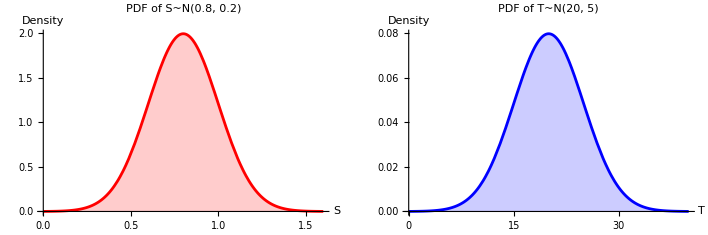

```mathematica
(*Define functions for Imax and m*)
Imax[T_]:=Exp[-((T-TI)^2)/γ];
m[T_]:=ma Exp[mb T]+mc;

(*Define probability function w for a given T and S*)
w[T_,S_]:=(Imax[T]*S)/(S+R0)-m[T];

(*Define grid size for the landscape*)
gridSize={50,50}; (*adjust for larger or smaller landscapes*)

(*Generate random values for T and S across the grid*)
meanT = 20;
varT = 5;
meanS = 0.8;
varS = 0.2 ;
Tgrid=RandomVariate[NormalDistribution[meanT,varT],gridSize];
Sgrid=RandomVariate[NormalDistribution[meanS,varS],gridSize];

(*Plot as a density plot*)
pdfPlotS=Plot[PDF[NormalDistribution[meanS,varS],x],{x,meanS - 4*varS,(meanS + 4*varS)},
	PlotLabel->Style[Text@StringJoin["PDF of S~N(",ToString[meanS],", ",ToString[varS],")"],14],
	Filling->Axis,PlotStyle->Red,AxesLabel->{"S","Density"},ImageSize->Medium];
pdfPlotT=Plot[PDF[NormalDistribution[meanT,varT],x],{x,0,40},
	PlotLabel->Style[Text@StringJoin["PDF of T~N(",ToString[meanT],", ",ToString[varT],")"],14],
	Filling->Axis,PlotStyle->Blue,AxesLabel->{"T","Density"},ImageSize->Medium];
	
(*Display the pdfs*)
SandTPDFS = GraphicsGrid[{{Style[pdfPlotS, FontSize->Scaled[0.04]],Style[pdfPlotT, FontSize->4]}}];
Show[SandTPDFS, ImageSize->6/2.54*300]
Export[relativePath["figs","temp-supply-wij-pdfs.pdf"],
	SandTPDFS, ImageSize -> 6/2.54*300, ImageResolution -> 1200];
```

## Standard landscape probabilities

We calculate the landscape probabilities and truncate them to be greater than zero, and if we consider a 2D space, we can plot all the options together.

```mathematica
(*Compute probabilities w_{i,j} across the landscape*)
(*Truncate landscape probabilities to be>=0*)
landscapeProbabilities=Table[Max[0,w[Tgrid[[i,j]],Sgrid[[i,j]]]],{i,gridSize[[1]]},{j,gridSize[[2]]}];

(*Heatmap for w_{i,j} values with Magma color scheme*)
heatmapW=ArrayPlot[landscapeProbabilities,
	ColorFunction->"Pastel",Mesh->False,
	PlotLabel->"Probability Landscape ( ≥ 0)",
	PlotLegends->Automatic];

(*Heatmap for T values with TemperatureMap color scheme*)
heatmapT=ArrayPlot[Tgrid,ColorFunction->"TemperatureMap",Mesh->False,
	PlotLabel->"Temperature (T) Landscape",PlotLegends->Automatic];

(*Heatmap for S values with purple gradient color scheme*)
heatmapS=ArrayPlot[Sgrid,ColorFunction->(Blend[{White,Purple},#]&),
	Mesh->False,PlotLabel->"Supply (S) Landscape",PlotLegends->Automatic];

(*Arrange the plots in a grid with T and S on the top row,w at double size on the second row*)
threeArray = GraphicsGrid[{{Style[heatmapT, 
	FontSize->Scaled[0.04]],Style[heatmapS, FontSize->4],
	Style[heatmapW, FontSize->4]}},Spacings->{2,1}];
Show[threeArray, ImageSize->6/2.54*300]
Export[relativePath["figs","temp-supply-probability-landscape.pdf"],threeArray, 
	ImageSize -> 6/2.54*300, ImageResolution -> 1200];
```

-Graphics-

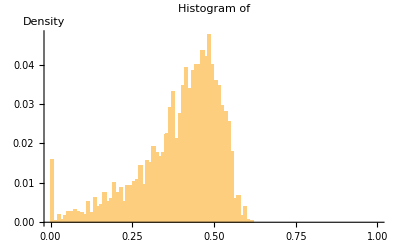

```mathematica
(*Flatten the landscape probabilities for density plot*)
flatProbabilities=Flatten[landscapeProbabilities];
hist=Histogram[flatProbabilities,{0, 1, 0.01},"Probability",
	PlotLabel->Style[Text@StringJoin["Histogram of "],14],
	AxesLabel->{"","Density"}];
hist
```

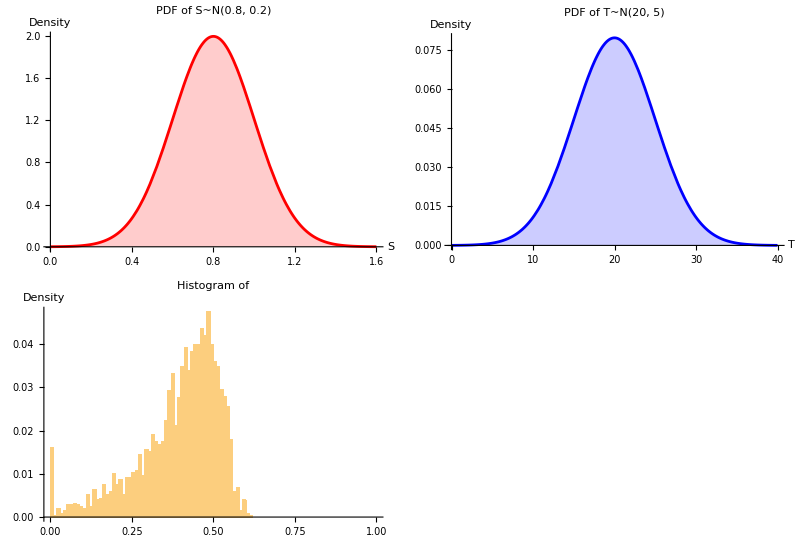

```mathematica
(*Display all three plots*)
GraphicsGrid[{{pdfPlotS,pdfPlotT},{hist}},Spacings->{2,1}]
```

## Now, from the values, calculate the normalized co-occurence probabilities.

So now, we want to state that each normalized probability is:

```mathematica
(*Step 1:Calculate normalized probabilities x_{i,j}*)
totalSum=Total[Total[landscapeProbabilities]];
normalizedProbabilities=landscapeProbabilities/totalSum;

(*Step 2:Calculate normalized co-occurrence probabilities *)
normalizedCoOccurrence=normalizedProbabilities^2;

(*Step 3:Plot normalized co-occurrence probabilities with a blue-to-red gradient*)
coOccurrenceHeatmap=ArrayPlot[normalizedCoOccurrence,ColorFunction->(Blend[{Blue,Red},#]&),Mesh->True,PlotLabel->"Normalized Co-Occurrence Probability Landscape ",PlotLegends->Automatic];

(*Display the heatmap*)
coOccurrenceHeatmap = GraphicsGrid[{{Style[coOccurrenceHeatmap, FontSize->Scaled[0.04]]}}];
coOccurrenceHeatmap
Export[relativePath["figs","cooccurence-heatmaps.pdf"],coOccurrenceHeatmap, ImageSize -> 6/2.54*300, ImageResolution -> 1200];
```

-Graphics-

### Enter subsection title here

#### Enter subsubsection title here

Enter text here. Enter TraditionalForm input for evaluation in a separate cell below:

```mathematica
∫xⅆx+√z
```

x^2/2+√z

Enter bulleted item text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter an inline formula like this: 2+2.

Enter numbered item text here.

Enter item paragraph text here.

Enter numbered subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for numbered display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter Wolfram Language program code below.

```mathematica
fun[x_]:=1
```

0

Enter text here. Enter non-Wolfram Language program code below.

DLLEXPORT int fun(WolframLibraryData libData, mreal A1, mreal *Res)
{
 mreal R0_0;
 mreal R0_1;
 R0_0 = A1;
 R0_1 = R0_0 * R0_0;
 *Res = R0_1;
 funStructCompile->WolframLibraryData_cleanUp(libData, 1);
 return 0;
}